## Theory

∇·j+(∂ρ)/(∂t)=0

Assuming kinetic part ~(p-eA)^2

∂_t (|ψ|)^2=∂_t ψ^*ψ+ψ^*∂_t ψ
=1/ⅈ[ψ^*H ψ-H ψ^* ψ]
=1/ⅈ[ψ^*(p^2/2-e p A)ψ-ψ(p^2/2-e p A)ψ^*]
=1/ⅈ[ψ^*((-∂^2)/2+ⅈ e ∂ A)ψ-ψ((-∂^2)/2-ⅈ e ∂ A)ψ^*]
=1/ⅈ[(∂ψ^*∂ψ-∂(ψ^*∂ψ))/2-(∂ψ∂ψ^*-∂(ψ∂ψ^*))/2+ψ^*ⅈ e ∂ A ψ+ψ ⅈ e ∂ A ψ^*]
=1/ⅈ[(-∂(ψ^*∂ψ-ψ∂ψ^*))/2+Aⅈ e (ψ^* ∂ ψ+ψ  ∂ ψ^*)]
=(-∂(ψ^*∂ψ-ψ∂ψ^*))/(2 ⅈ)+A e (ψ^* ∂ ψ+ψ ∂  ψ^*)
=-∂Im(ψ^*∂ψ)+∂A e (|ψ|)^2
=∇·(-Im(ψ^*∂ψ)+A e (|ψ|)^2)
=|e=-1|=-∇·(Im(ψ^*∂ψ)+A (|ψ|)^2)=-∇·j

Re(ψ^* e v ψ)
=Im(ⅈ ψ^* e v ψ)
=Im(ⅈ ψ^* e (p-e A) ψ)
=Im(ⅈ ψ^* e (-ⅈ ∂-e A) ψ)
=Im( ψ^* e  ∂ ψ-ⅈ (|ψ|)^2 e^2  A)
=e Im( ψ^*∂ψ)-(|ψ|)^2 e^2 A

So in the case of e=-1, we get:

=- Im( ψ^*∂ψ)-(|ψ|)^2 A

Using the first equation we get:

∇·j+(∂ρ)/(∂t)

## Implementation

```mathematica
ϵ=0.01;
zero=0;
(*corresponds to previewMask()*)
val2int[f_]:=zero+If[f[[1]]>ϵ,1,If[f[[1]]<-ϵ,2,If[Length[f]<2,0,If[f[[2]]>ϵ,3,If[f[[2]]<-ϵ,4,If[Length[f]<3,0,If[f[[3]]>ϵ,5,If[f[[3]]<-ϵ,6,0]]]]]]]];
minMax=zero+{0,6};
color=Blend[{Transparent,(*x>0*)Red,(*x<0*)Blue,(*y>0*)Green,(*y<0*)Purple,(*z>0*)Black,(*z<0*)Yellow},Rescale[#,minMax]]&;
```

```mathematica
n=128;
n2=n/2;
CAP=n/4;
NS=IntegerPart[0.5 CAP(* /1.54*)];(*8, r3*)
SD=IntegerPart[0.5 NS];(*5,r2*)
DT=IntegerPart[0.5 SD];(*3,r1*)
```

```mathematica
(*real grid - example grid conversion*)
dx=0.6;
realGrid=2048;
realRatio=realGrid/n;
ticksCount=14;

rng={0,n-1};
rng2=realRatio rng;
divs=Most@Rest@FindDivisions[rng-(Last@rng+1)/2,ticksCount];

ticks= realRatio (n2-0.5+divs);
ticksI={ticks, realRatio ((Last@rng+1)/2+divs)}ᵀ;
ticksP=dx realRatio  divs ;
ticksP={ticks,ticksP-Mean[ticksP]}ᵀ;
```

```mathematica
(*outwards oriented point boundary at iat*)
Rn[i_,il_,ir_]:=(i>=il&&i<ir);
Rn2[i_,il_,ir_]:=Rn[i,il,ir]||Rn[i,-ir,-il];

(*because zero is not at n2*dx but at (n2-0.5)*dx*)
PointB[i_,iat_]:=If[i==iat-1,Sign[i],0];
PointB2[i_,iat_]:=If[i==iat-1||i==-iat,Sign[i],0];
(*outwards oriented line boundary at jat from il to ir*)
SegmentB[i_,j_,jat_,il_,ir_]:=If[Rn[i,il,ir],PointB[j,jat],0];
SegmentBi2[i_,j_,jat_,il_,ir_]:=If[Rn2[i,il,ir],PointB[j,jat],0];
SegmentBj2[i_,j_,jat_,il_,ir_]:=If[Rn[i,il,ir],PointB2[j,jat],0];
SegmentBi2j2[i_,j_,jat_,il_,ir_]:=If[Rn2[i,il,ir],PointB2[j,jat],0];

(*outwards oriented plane boundary at kat from il to ir and jl to jr*)
PatchB[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn[i,il,ir],SegmentB[j,k,kat,jl,jr],0];
PatchBi2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn2[i,il,ir],SegmentB[j,k,kat,jl,jr],0];
PatchBj2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn[i,il,ir],SegmentBi2[j,k,kat,jl,jr],0];
PatchBk2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn[i,il,ir],SegmentBj2[j,k,kat,jl,jr],0];
PatchBi2j2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn2[i,il,ir],SegmentBi2[j,k,kat,jl,jr],0];
PatchBi2k2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn2[i,il,ir],SegmentBj2[j,k,kat,jl,jr],0];
PatchBj2k2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn[i,il,ir],SegmentBi2j2[j,k,kat,jl,jr],0];
PatchBi2j2k2[i_,j_,k_,kat_,il_,ir_,jl_,jr_]:=If[Rn2[i,il,ir],SegmentBi2j2[j,k,kat,jl,jr],0];
```

### 3D

```mathematica
N2S2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,NS,0,SD,0,DT-1]+PatchBi2j2k2[k,j,i,NS,0,SD,0,DT-1],PatchBi2j2k2[k,i,j,NS,0,SD,0,DT-1]+PatchBi2j2k2[i,k,j,NS,0,SD,0,DT-1],PatchBi2j2k2[i,j,k,NS,0,SD,0,DT-1]+PatchBi2j2k2[j,i,k,NS,0,SD,0,DT-1]};
N2D2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,SD,SD,NS,0,DT-1]+PatchBi2j2k2[k,j,i,SD,SD,NS,0,DT-1],PatchBi2j2k2[k,i,j,SD,SD,NS,0,DT-1]+PatchBi2j2k2[i,k,j,SD,SD,NS,0,DT-1],PatchBi2j2k2[i,j,k,SD,SD,NS,0,DT-1]+PatchBi2j2k2[j,i,k,SD,SD,NS,0,DT-1]};
N2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,DT-1,NS,DT-1,SD]+PatchBi2j2k2[k,j,i,DT,DT-1,NS,DT-1,SD],PatchBi2j2k2[k,i,j,DT,DT-1,NS,DT-1,SD]+PatchBi2j2k2[i,k,j,DT,DT-1,NS,DT-1,SD],
PatchBi2j2k2[i,j,k,DT,DT-1,NS,DT-1,SD]+PatchBi2j2k2[j,i,k,DT,DT-1,NS,DT-1,SD]};
S2D2e[i_,j_,k_]:=
{PatchBi2j2k2[j,k,i,SD,NS,CAP,0,DT]+PatchBi2j2k2[k,j,i,SD,NS,CAP,0,DT],
PatchBi2j2k2[k,i,j,SD,NS,CAP,0,DT]+PatchBi2j2k2[i,k,j,SD,NS,CAP,0,DT],
PatchBi2j2k2[i,j,k,SD,NS,CAP,0,DT]+PatchBi2j2k2[j,i,k,SD,NS,CAP,0,DT]};
S2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,NS,CAP,DT,SD]+PatchBi2j2k2[k,j,i,DT,NS,CAP,DT,SD],
PatchBi2j2k2[k,i,j,DT,NS,CAP,DT,SD]+PatchBi2j2k2[i,k,j,DT,NS,CAP,DT,SD],PatchBi2j2k2[i,j,k,DT,NS,CAP,DT,SD]+PatchBi2j2k2[j,i,k,DT,NS,CAP,DT,SD]};
D2T2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,DT,SD,CAP,SD,CAP],
PatchBi2j2k2[k,i,j,DT,SD,CAP,SD,CAP],
PatchBi2j2k2[i,j,k,DT,SD,CAP,SD,CAP]};
S2CAP2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,CAP,0,DT,0,SD]+PatchBi2j2k2[k,j,i,CAP,0,DT,0,SD],
PatchBi2j2k2[k,i,j,CAP,0,DT,0,SD]+PatchBi2j2k2[i,k,j,CAP,0,DT,0,SD],
PatchBi2j2k2[i,j,k,CAP,0,DT,0,SD]+PatchBi2j2k2[j,i,k,CAP,0,DT,0,SD]}
D2CAP2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,CAP,SD,CAP,0,DT]+PatchBi2j2k2[k,j,i,CAP,SD,CAP,0,DT],
PatchBi2j2k2[k,i,j,CAP,SD,CAP,0,DT]+PatchBi2j2k2[i,k,j,CAP,SD,CAP,0,DT],
PatchBi2j2k2[i,j,k,CAP,SD,CAP,0,DT]+PatchBi2j2k2[j,i,k,CAP,SD,CAP,0,DT]}
T2CAP2e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,CAP,DT,CAP,DT,CAP](*+PatchBi2j2k2[k,j,i,CAP,DT,CAP,DT,CAP]*),
PatchBi2j2k2[k,i,j,CAP,DT,CAP,DT,CAP](*+PatchBi2j2k2[i,k,j,CAP,0,DT,CAP,DT,CAP]*),
PatchBi2j2k2[i,j,k,CAP,DT,CAP,DT,CAP](*+PatchBi2j2k2[j,i,k,CAP,0,DT,CAP,DT,CAP]*)}
```

```mathematica
(*plot b*)
Manipulate[
Graphics3D[Raster3D[Table[val2int@(If[n2s,N2S2e[i-n2,j-n2,k-n2],0]+If[n2d,N2D2e[i-n2,j-n2,k-n2],0]+If[n2t,N2T2e[i-n2,j-n2,k-n2],0]),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},PlotRangePadding->0.5,ImageSize->Large,Axes->True],{n2s,{True,False}},{n2d,{True,False}},{n2t,{True,False}}]
```

```mathematica
(*plot c*)
Manipulate[
Graphics3D[Raster3D[Table[val2int@(If[s2d,S2D2e[i-n2,j-n2,k-n2],0]+If[s2t,S2T2e[i-n2,j-n2,k-n2],0]+If[d2t,D2T2e[i-n2,j-n2,k-n2],0]),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},PlotRangePadding->0.5,ImageSize->Large,Axes->True],{s2d,{True,False}},{s2t,{True,False}},{d2t,{True,False}}]
```

```mathematica
(*all regions*)
Manipulate[
Graphics3D[Raster3D[Table[val2int@(If[n2s,N2S2e[i-n2,j-n2,k-n2],0]
+If[n2d,N2D2e[i-n2,j-n2,k-n2],0]
+If[n2t,N2T2e[i-n2,j-n2,k-n2],0]
+If[s2d,S2D2e[i-n2,j-n2,k-n2],0]
+If[s2t,S2T2e[i-n2,j-n2,k-n2],0]
+If[d2t,D2T2e[i-n2,j-n2,k-n2],0]
+If[s2cap,S2CAP2e[i-n2,j-n2,k-n2],0]
+If[d2cap,D2CAP2e[i-n2,j-n2,k-n2],0]
+If[t2cap,T2CAP2e[i-n2,j-n2,k-n2],0]),{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},PlotRangePadding->0.5,ImageSize->Large,Axes->True],{n2s,{True,False}},{n2d,{True,False}},{n2t,{True,False}},{s2d,{True,False}},{s2t,{True,False}},{d2t,{True,False}},{s2cap,{True,False}},{d2cap,{True,False}},{t2cap,{True,False}}]
```

### 2D

```mathematica
N2Se[i_,j_]:={SegmentBi2j2[j,i,NS,0,SD],SegmentBi2j2[i,j,NS,0,SD]};
S2De[i_,j_]:={SegmentBi2j2[j,i,SD,NS,CAP],SegmentBi2j2[i,j,SD,NS,CAP]};

S2DeSYM[i_,j_]:={SegmentB[j,i,SD,NS,CAP]-SegmentB[-j-1,-i-1,SD,NS,CAP],SegmentB[i,j,SD,NS,CAP]-SegmentB[-i-1,-j-1,SD,NS,CAP]};
S2DeASYM[i_,j_]:={-SegmentB[j,-i-1,SD,NS,CAP]+SegmentB[-j-1,i,SD,NS,CAP],-SegmentB[i,-j-1,SD,NS,CAP]+SegmentB[-i-1,j,SD,NS,CAP]};

N2De[i_,j_]:={SegmentBi2j2[j,i,SD,SD,NS],SegmentBi2j2[i,j,SD,SD,NS]};

(*N2DeSYM[i_,j_]:={SegmentB[j,i,SD,SD,NS]-SegmentB[-j-1,-i-1,SD,SD,NS],SegmentB[i,j,SD,SD,NS]-SegmentB[-i-1,-j-1,SD,SD,NS]};
N2DeASYM[i_,j_]:={-SegmentB[j,-i-1,SD,SD,NS]+SegmentB[-j-1,i,SD,SD,NS],-SegmentB[i,-j-1,SD,SD,NS]+SegmentB[-i-1,j,SD,SD,NS]};*)
N2DeSYM[i_,j_]:={SegmentB[j+1,i,SD,SD,NS+1]-SegmentB[-j,-i-1,SD,SD,NS+1], SegmentB[i+1,j,SD,SD,NS+1]-SegmentB[-i,-j-1,SD,SD,NS+1]};
N2DeASYM[i_,j_]:={-SegmentB[j+1,-i-1,SD,SD,NS+1]+SegmentB[-j,i,SD,SD,NS+1],-SegmentB[i+1,-j-1,SD,SD,NS+1]+SegmentB[-i,j,SD,SD,NS+1]};


S2CAPe[i_,j_]:={SegmentBi2j2[j,i,CAP,0,SD],SegmentBi2j2[i,j,CAP,0,SD]};
D2CAPe[i_,j_]:={SegmentBi2j2[j,i,CAP,SD,CAP],SegmentBi2j2[i,j,CAP,SD,CAP]};
```

```mathematica
Table[N2DeSYM[i-n2,j-n2],{i,0,n-1},{j,0,n-1}]
```

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},12,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},126,{1}}
 |  |  |  |

```mathematica
CoolColor[ z_ ] :=RGBColor[0.5+z/2,0.5-z/2,0.5+z/2,If[Abs[z]==1,1,0]];
CoolColor2[ z_ ] :=RGBColor[0.5+z/2,0.5+z/2,0.5-z/2,If[Abs[z]==1,1,0]];
Draw:=Show[{ArrayPlot[Table[#[i-n2,j-n2],{i,0,n-1},{j,0,n-1}][[All,All,1]],ColorFunction->CoolColor,ColorFunctionScaling->False,PlotLegends->Automatic],
 ArrayPlot[Table[#[i-n2,j-n2],{i,0,n-1},{j,0,n-1}][[All,All,2]],ColorFunction->CoolColor2,ColorFunctionScaling->False,PlotLegends->Automatic] }]&;
```

```mathematica
RGBColor[1,0,1]
RGBColor[0,1,0]
RGBColor[1,1,0]
RGBColor[0,0,1]
```

RGBColor[1, 0, 1]

RGBColor[0, 1, 0]

RGBColor[1, 1, 0]

RGBColor[0, 0, 1]

```mathematica
Draw@N2Se

Draw@S2De
Draw@S2DeSYM
Draw@S2DeASYM

Draw@N2De
Draw@N2DeASYM
Draw@N2DeSYM

Draw@S2CAPe
Draw@D2CAPe
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Manipulate[
ArrayPlot[Reverse@Table[val2int@(If[n2s,N2Se[i-n2,j-n2],0]+If[s2dS,S2DeSYM[i-n2,j-n2],0]+If[n2dS,N2DeSYM[i-n2,j-n2],0]+If[s2dA,S2DeASYM[i-n2,j-n2],0]+If[n2dA,N2DeASYM[i-n2,j-n2],0]+If[s2cap,S2CAPe[i-n2,j-n2],0]+If[d2cap,D2CAPe[i-n2,j-n2],0]),{i,0,n-1},{j,0,n-1}],ColorFunction->color,
ColorFunctionScaling->False,
FrameLabel->{{"y [au]","j [index]"},{"i [index]","x [au]"}},FrameTicks->{{ticksI,ticksP},{ticksP,ticksI}},
DataRange->{rng2,rng2},
DataReversed->True,
GridLines->{{(n2-0.5) realRatio},{(n2-0.5) realRatio}},
PlotRangePadding->0,
ImageSize->Large
],{{n2s,False},{True,False}},{{n2dS,True},{True,False}},{{n2dA,True},{True,False}},{{s2dS,False},{True,False}},{{s2dA,False},{True,False}},{{s2cap,False},{True,False}},{{d2cap,False},{True,False}}]
```

### 1D

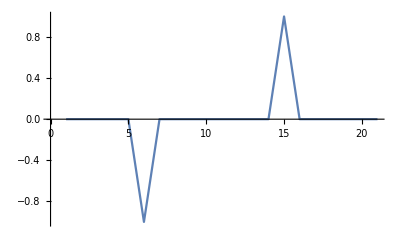

```mathematica
ListLinePlot[Table[PointB2[i-10,5],{i,0,20}]]
```

### Other

#### ManhatanSphere

```mathematica
Cube3e[i_,j_,k_]:={
PatchBi2j2k2[j,k,i,CAP,0,CAP,0,CAP],
PatchBi2j2k2[k,i,j,CAP,0,CAP,0,CAP],
PatchBi2j2k2[i,j,k,CAP,0,CAP,0,CAP]}
Graphics3D[Raster3D[Table[val2int@Cube3e[i-n2,j-n2,k-n2],{i,0,n-1},{j,0,n-1},{k,0,n-1}],ColorFunction->color],AxesLabel->{k,j,i},Ticks->{ticks,ticks,ticks},PlotRangePadding->0.5,ImageSize->Large,Axes->True]
```

```mathematica
Cube2e[i_,j_]:={
SegmentBi2j2[j,i,CAP/2,0,CAP/2],
SegmentBi2j2[i,j,CAP/2,0,CAP/2]};
MatrixPlot[Reverse@Table[val2int@Cube2e[i-n2,j-n2],{i,0,n-1},{j,0,n-1}],ColorFunction->color,ColorFunctionScaling->False,FrameLabel->{{j,y},{x,i}},FrameTicks->{{ticks,ticks2},{ticks2,ticks}},DataRange->{rng2,rng2},DataReversed->True,GridLines->{{n2-0.5},{n2-0.5}},PlotRangePadding->0,ImageSize->Large]
```